```mathematica
Binomial[4, 2]
```

6

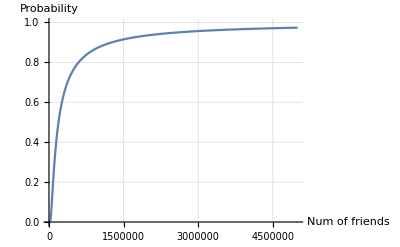

```mathematica
Plot[Binomial[n-1,n-365] / Binomial[365+n-1,n],{n, 365, 5000000},AxesLabel->{"Num of friends","Probability"},PlotRange->{0,1}, GridLines->Automatic]
```

```mathematica
(*If using ListLogPlot it takes much time to calculate.*)(*ListLogPlot[Table[Binomial[n-1,n-365]/Binomial[365+n-1,n],{n,365,10000000}]]*)
```